### Results from a calculation of K from the kappa J-V relation assuming 1≪ϕ^—≪R_B.

```mathematica
ratio[κ_]:=Gamma[κ]/((κ-3/2)^(1/2)Gamma[κ-1/2])
```

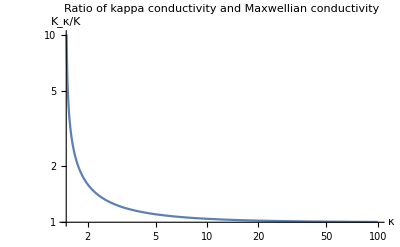

```mathematica
LogLogPlot[ratio[κ],{κ,3/2,100},PlotRange->{{3/2,100},{1,10}},AxesLabel->{"κ","K_κ/K"},PlotLabel->"Ratio of kappa conductivity and Maxwellian conductivity"]
```